Export::nodir: Directory "C:\\Users\\tvw\\Documents\\Electron-Transport-LAO-STO\\NanowireCalculations\\" does not exist.

OpenWrite::noopen: Cannot open "C:\\Users\\tvw\\Documents\\Electron-Transport-LAO-STO\\NanowireCalculations\\testList.txt".

$Failed

-Graphics3D-

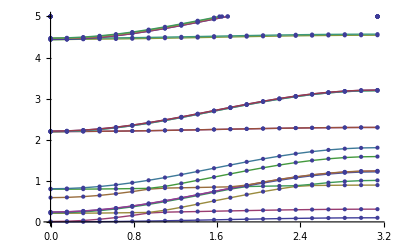

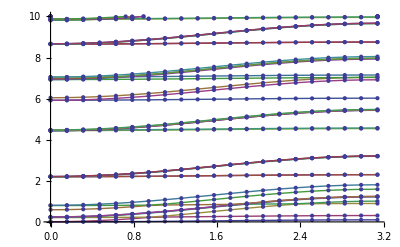

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=5;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=8;
NN=4;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=20;

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];

Initialize[];
(*firstGuess=Flatten[Table[
	 1,
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Total)firstGuess;*)
firstGuess={9.579710741657639*^-6,0.007423119351984888,0.4993886512028265,1.2577130576648647,0.4993920606435739,0.00742341496158461,9.685437175503882*^-6,-0.00001254812734658749,-0.00001742665038765614,0.00028472660458278754,0.0009270707298519518,0.00028473324189772794,-0.00001740848430610889,-0.000012530647372770232,-5.7290454515409656*^-6,-0.000010584227126347517,-0.000013752212740143942,-0.000014747415875497743,-0.000013752210158716902,-0.000010584217418934225,-5.729037260029024*^-6,-2.6120917409144827*^-6,-4.8265160108995165*^-6,-6.306139445778352*^-6,-6.82570372113358*^-6,-6.306139445420135*^-6,-4.826516009267943*^-6,-2.61209174147271*^-6};

{listvals,errorList}=SelfConsistentDistribution[firstGuess,.000000005];
Export["NanowireCalculations/testList.txt",listvals,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,5,bandList]
BandStructurePlot[0,10,bandList]
```

```mathematica
PlotFullSpaceDistribution[listvals]
```

-Graphics3D-

```mathematica
listvals//Total
totalCharge/2
```

2.27273

-2.27364